```mathematica
Solving OFAST
```

```mathematica
(*
Copyright (c) 2016 F.X.Coudert& G.Fraux 

Permission is hereby granted,free of charge,to any person obtaining a copy 
of this software and associated documentation files (the "Software"),to deal 
in the Software without restriction,including without limitation the rights 
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell copies of 
the Software,and to permit persons to whom the Software is furnished to do so,
 subject to the following conditions:

The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND EXPRESS OR
   IMPLIED INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY, 
    FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL 
   THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
   LIABILITY, WHETHER IN AN ACTION OF CONTRACT TORT OR OTHERWISE ARISING FROM,
    OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.
*)

Get["OFAST`"];
```

```mathematica
(* These are the values for short alkanes in RPMZn-3,the transition is close->open *)
thetaC2=0.905166;
NC2=4.81869;
KC2=1.74415;

thetaC3=2.88575;
NC3=8.99765;
KC3=41.9608;

thetaC4=27.2624;
NC4=5.86621;
KC4=698.995;

DeltaF = -30000;

logspace[a_,b_,n_]:=10.0^Range[Log10[a],Log10[b],(Log10[b]-Log10[a])/(n-1)];
```

### C3H8 / C2H6

```mathematica
selectivityAtComposition[yB_]:=Table[{pp,SolveOFAST[thetaC3, thetaC2,KC3,NC3,KC2,NC2,DeltaF,yB,pp][[1]]},{pp,logspace[0.001, 0.8, 100]}];
selectComp01 = selectivityAtComposition[0.1];
selectComp05 = selectivityAtComposition[0.5];
selectComp09 = selectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C3-C2-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C3-C2-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C3-C2-0.9.dat".

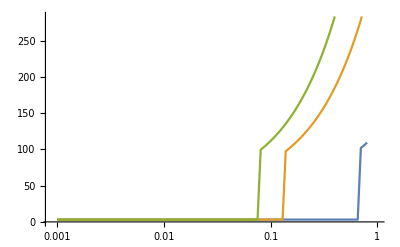

```mathematica
Export["results/OFAST-C3-C2-0.1.dat", selectComp01];
Export["results/OFAST-C3-C2-0.5.dat", selectComp05];
Export["results/OFAST-C3-C2-0.9.dat", selectComp09];
ListLogLinearPlot[{selectComp01, selectComp05, selectComp09}, Joined->True]
```

### C4H10 / C2H6

```mathematica
(* Ignoring the second jump for the C4H10 isotherm *)
selectivityAtComposition[yB_]:=Table[{pp,SolveOFAST[thetaC4, thetaC2,KC4,NC4,KC2,NC2,DeltaF,yB,pp][[1]]},{pp,logspace[0.001, 0.7, 100]}];
selectComp01 = selectivityAtComposition[0.1];
selectComp05 = selectivityAtComposition[0.5];
selectComp09 = selectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C2-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C2-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C2-0.9.dat".

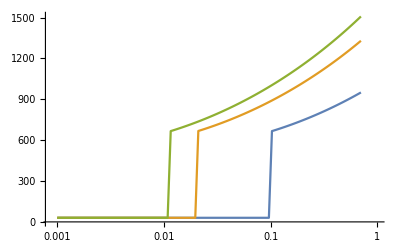

```mathematica
Export["results/OFAST-C4-C2-0.1.dat", selectComp01];
Export["results/OFAST-C4-C2-0.5.dat", selectComp05];
Export["results/OFAST-C4-C2-0.9.dat", selectComp09];
ListLogLinearPlot[{selectComp01, selectComp05, selectComp09}, Joined->True]
```

### C4H10 / C3H8

```mathematica
selectivityAtComposition[yB_]:=Table[{pp,SolveOFAST[thetaC4, thetaC3,KC4,NC4,KC3,NC3,DeltaF,yB,pp][[1]]},{pp, logspace[0.001, 0.8, 100]}];
selectComp01 = selectivityAtComposition[0.1];
selectComp05 = selectivityAtComposition[0.5];
selectComp09 = selectivityAtComposition[0.9];
```

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C3-0.1.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C3-0.5.dat".

Export::nodir: Directory "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/" does not exist.

OpenWrite::noopen: Cannot open "/home/guillaume/Dropbox/Partage TGU/Guillaume/OFAST/SI/results/OFAST-C4-C3-0.9.dat".

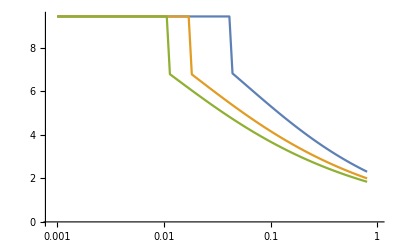

```mathematica
Export["results/OFAST-C4-C3-0.1.dat", selectComp01];
Export["results/OFAST-C4-C3-0.5.dat", selectComp05];
Export["results/OFAST-C4-C3-0.9.dat", selectComp09];
ListLogLinearPlot[{selectComp01,  selectComp05, selectComp09}, Joined->True]
```